```mathematica
Needs["MaTeX`"];
ConfigureMaTeX["pdfLaTeX" -> "c:\\Program Files\\MiKTeX\\miktex\\bin\\x64\\pdflatex.exe"];
ConfigureMaTeX["Ghostscript" -> "c:\\Program Files\\GhostScript\\gs9.54.0\\bin\\gswin64c.exe"];
ResourceFunction["MaTeXInstall"][];

SetOptions[MaTeX,"Preamble"->{"\\usepackage{color}",
"\\definecolor{črna}{rgb}{0,0,0}",
"\\definecolor{modra}{rgb}{0,0,1}",
"\\definecolor{zelena}{rgb}{0,1,0}",
"\\definecolor{rdeča}{rgb}{1,0,0}",
"\\definecolor{cian}{rgb}{0,1,1}",
"\\definecolor{magenta}{rgb}{1,0,1}",
"\\definecolor{rumena}{rgb}{1,1,0}",
"\\definecolor{bela}{rgb}{1,1,1}",
"\\definecolor{siva}{rgb}{.3,.3,.3}"
}];
Graphics[Text[MaTeX["\\color{red}{\\mathbf{\\hat{i}}=\\mathbf{\\left(1,0\\right)}}",FontSize->50],{2,1.3}]]
```

-Graphics-

```mathematica
MaTeX["\\sum_{k=1}^{15} \\frac{1}{k^2} = \\frac{\\pi^2}{6}",FontSize->24]
```

-Graphics-

```mathematica
Style[Red,Rotate[MaTeX["\\sum_{k=1}^{15} \\frac{1}{k^2} = \\frac{\\pi^2}{6}",FontSize->24],10]]
```

Style[RGBColor[1, 0, 0],MaTeX[\sum_{k=1}^{15} \frac{1}{k^2} = \frac{\pi^2}{6},FontSize→24,RGBColor[1, 0, 0]]]

-Graphics-

```mathematica
Needs["MaTeX`"];
MaTeX[HoldForm@Integrate[Exp[-x],{x,0,Infinity}]]
```

pdfLaTeX is not found at C:\Program Files\MiKTeX 2.9\miktex\bin\x64\pdflatex.exe

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

Ghostscript is not found at C:\Program Files\gs\gs9.27\bin\gswin64c.exe

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

$Failed

Ghostscript is not found at C:\Program Files\gs\gs9.27\bin\gswin64c.exe

Click here for documentation on configuring MaTeX.

{CacheSize→100,WorkingDirectory→Automatic,Ghostscript→C:\Program Files\gs\gs9.27\bin\gswin64c.exe,pdfLaTeX→c:\Program Files\MiKTeX\miktex\bin\x64\pdflatex.exe}

```mathematica
<<MaTeX`

MaTeX["\\sin^2 \\varphi + \\cos^2 \\varphi = 1",Magnification->2]

MaTeX[Sin[x]+O[x]^8,Magnification->2]
```

pdfLaTeX is not found at C:\Program Files\MiKTeX 2.9\miktex\bin\x64\pdflatex.exe

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

Ghostscript is not found at C:\Program Files\gs\gs9.27\bin\gswin64c.exe

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

pdfLaTeX is not found at C:\Program Files\MiKTeX 2.9\miktex\bin\x64\pdflatex.exe

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

Ghostscript is not found at C:\Program Files\gs\gs9.27\bin\gswin64c.exe

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

$Failed

pdfLaTeX is not found at C:\Program Files\MiKTeX 2.9\miktex\bin\x64\pdflatex.exe

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

Ghostscript is not found at C:\Program Files\gs\gs9.27\bin\gswin64c.exe

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

$Failed

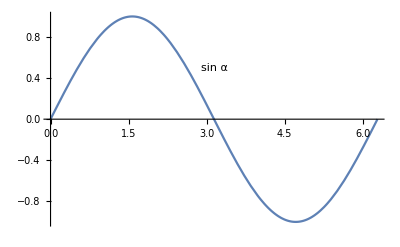

```mathematica
Plot[Sin[x],{x,0,2 Pi},Epilog->Text[Style[ToExpression["\\sin\\alpha",TeXForm,HoldForm],Large],{Pi,.5}]]
```

```mathematica
Plot[Sin[x], {x, 0, 2 Pi}, 
 Epilog -> 
  Text[Style[
    ToExpression["\\sin\\alpha", TeXForm, HoldForm], Large], {Pi, .5}]]
```

-Graphics-

```mathematica
ToExpression["\\varphi\\=alpha", TeXForm, HoldForm]
```

Import::texerr: Error: Please use \mathaccent for accents in math mode.

$Failed

```mathematica
ConfigureMaTeX[\"pdfLaTeX\" -> \"C:\\Program Files\\MiKTeX\\miktex\\bin\\x64"]
```

```mathematica
ConfigureMaTeX[\"Ghostscript\" -> \"C:\\Program Files\\GhostScript\\gs9.54.0\\"]
```

-Graphics-

-Graphics-